# vitrimer τα

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.00015_rho1.6_kpeak.dat"]
```

```mathematica
fsFileName=FileNames["Fs_T*_rho*_kpeak.dat","/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/"];
```

```mathematica
fsFileName[[1]]
```

/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.00015_rho1.6_kpeak.dat

```mathematica
rhoValues=N[Sort[DeleteDuplicates[Flatten[StringCases[FileBaseName/@fsFileName,(*strip directory+extension*)___~~"rho"~~r:NumberString~~___:>ToExpression[r]]]]]]
```

{0.92333,1.2021,1.42239,1.50772,1.6,1.69997,1.80845,1.97531,2.42954,2.5155,2.8125}

```mathematica
ToString[rhoValues[[1]]]
```

0.92333

```mathematica
temperatures=Table[Reverse[Sort[DeleteDuplicates[ToExpression[StringReplace[Flatten[StringCases[FileBaseName/@FileNames["Fs_T*_rho"<>ToString[rhoValues[[rho]]]<>"_kpeak.dat","/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/"],(*strip directory+extension*)___~~"T"~~r:(DigitCharacter..~~(("."~~DigitCharacter..)...)~~(("e"|"E")~~("+"|"-")~~DigitCharacter..)...)~~"_rho"<>ToString[rhoValues[[rho]]]~~___:>r]],"e"->"*^"]]]]],{rho,Length[rhoValues]}]
```

{{0.65,0.5,0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,1/50000,1/100000,1/125000,6.5×10^-6,1/200000,3.5×10^-6,1/500000,1.5×10^-6,1/1000000,1/1250000,7/10000000,3/5000000,1/2000000,2.5×10^-7,1/10000000,7.5×10^-8,1/20000000,2.5×10^-8,1/100000000,7.5×10^-9,1/200000000,2.5×10^-9,1/1000000000},{0.15,0.1,0.09,0.07,0.06,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,3/100000,1/50000,1/100000,1/125000,1/200000,1/500000,1.25×10^-6,1/1000000,1/1250000,3/5000000,1/2000000,2.5×10^-7,1/10000000,7.5×10^-8,1/20000000,2.5×10^-8,1/100000000},{0.15,0.1,0.09,0.08,0.07,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00025,0.0001,1/20000,1/100000,1/125000,1/200000,1/500000,1/1000000,7.5×10^-7,1/2000000,2.5×10^-7,1/10000000,7.5×10^-8,1/20000000,2.5×10^-8,1/100000000},{0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00075,0.0005,0.00025,0.0001,1/20000,0.000025,1/100000,7.5×10^-6,3/500000,1/200000,2.5×10^-6,1/1000000},{0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.0055,0.005,0.0045,0.004,0.0035,0.0033,0.0022,0.002,0.0013,0.001,0.0009,0.0003,0.00015,0.0001,7/100000,1/20000,3/100000,1/50000,1/100000,1/200000},{0.15,0.1,0.09,0.08,0.07,0.06,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0038,0.0037,0.0036,0.0034,0.0033,0.0032,0.0031,0.003,0.0029,0.0028,0.0027,0.0025,0.0022,0.002,0.0018,0.0017,0.0015,0.0014,0.0013,0.0012,0.0011,0.00105,0.001,0.00095},{0.3,0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.009,0.0085,0.00825,0.008,0.00775,0.0075,0.00725,0.007,0.0065,0.0063,0.0061,0.0059,0.00575,0.0055,0.00535,0.0051,0.00505,0.005,0.0035,0.003,0.0025,0.002,0.001},{0.15,0.09,0.08,0.07,0.06,0.05,0.045,0.044,0.04,0.035,0.033,0.032,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001},{0.3,0.15,0.1,0.09,0.08,0.07,0.0695,0.069,0.0685,0.068,0.065,0.064,0.063,0.062,0.061,0.06,0.05,0.04,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.001},{0.15,0.1,0.09,0.08,0.07,0.069,0.068,0.067,0.066,0.065,0.064,0.063,0.062,0.061,0.06,0.055,0.054,0.053,0.0525,0.052,0.0515,0.051,0.05,0.045,0.04,0.035},{0.3,0.15,0.1,0.09,0.08,0.07,0.065,0.0625,0.061,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.001}}

```mathematica
Table[Length[temperatures[[r]]]-Length[fs[[r]]],{r,Length[rhoValues]}]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[FileNames["Fs_T*_rho"<>ToString[rhoValues[[r]]]<>"_kpeak.dat","/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/"],{r,-1,-1}][[1]]
```

{/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.007_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.008_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.015_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.01_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.03_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.05_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.061_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0625_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.065_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.06_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.07_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.08_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.09_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.15_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho2.8125_kpeak.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.3_rho2.8125_kpeak.dat}

```mathematica
fs=Table[Import[#,"Data"]&/@FileNames["Fs_T*_rho"<>ToString[rhoValues[[r]]]<>"_kpeak.dat","/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/"],{r,Length[rhoValues]}];
```

```mathematica
Length[fs[[5]]]
```

33

```mathematica
0.2/(1/0.8)
```

0.16

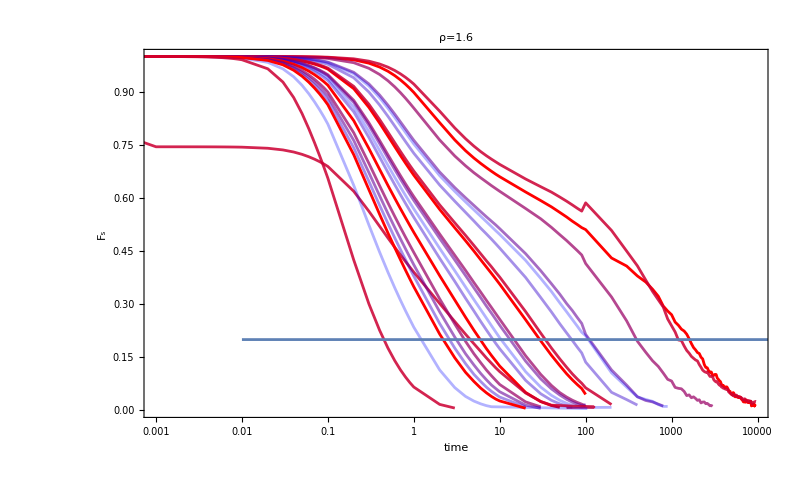

```mathematica
Table[Show[ListLogLinearPlot[fs[[r,;;20,;;,1;;2]],ImageSize->800,PlotRange->{{0.001,All},All},PlotStyle->redBluePlotConfig[6],PlotLabel->"ρ="<>ToString[rhoValues[[r]]],Joined->True,FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}]],{r,5,5}]
```

```mathematica
temperatures[[-1]]
```

{0.3,0.15,0.1,0.09,0.08,0.07,0.065,0.0625,0.061,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.001}

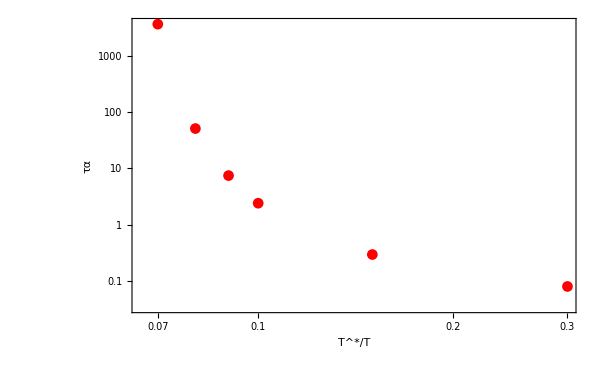

```mathematica
Show[ListLogLogPlot[Table[Table[{temperatures[[r,T]],tauAlpha[[r,T]]},{T,Length[tauAlpha[[r]]]}],{r,-1,-1}],FrameLabel->{"T^*/T","τα"},ImageSize->600,PlotRange->{All,All},Joined->False,PlotStyle->redBluePlotConfig[Length[rhoValues]]]]
```

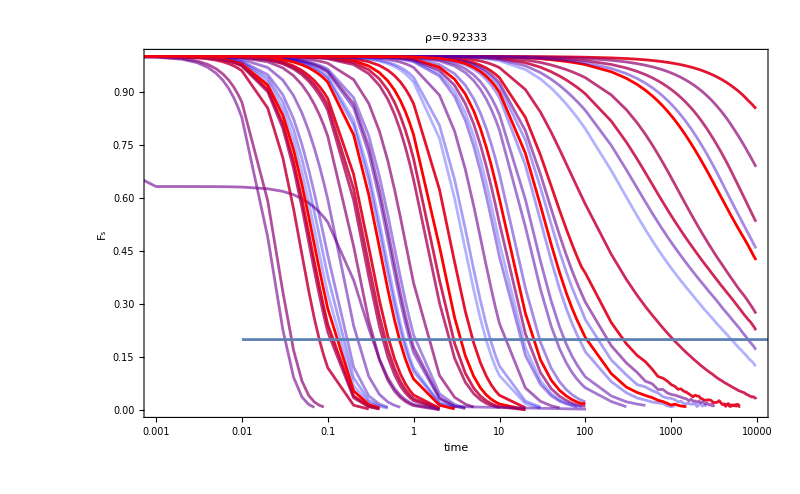
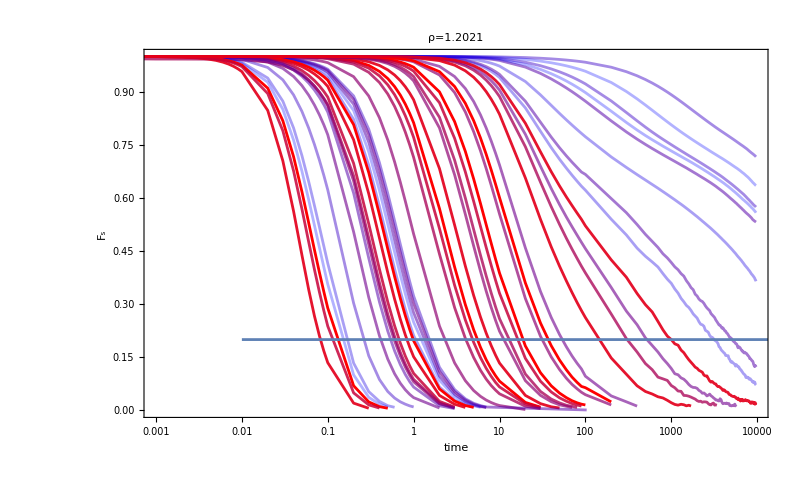
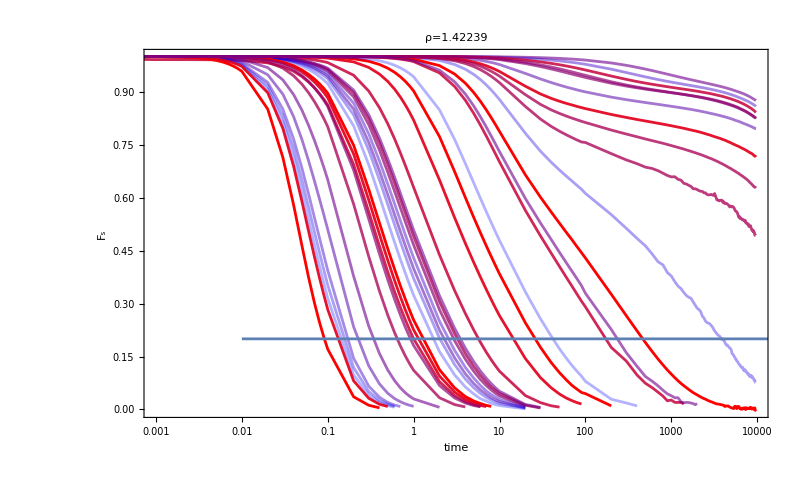
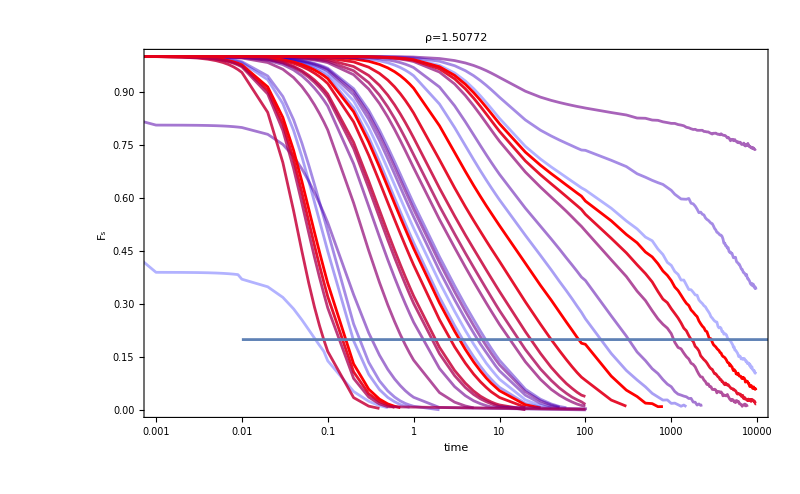
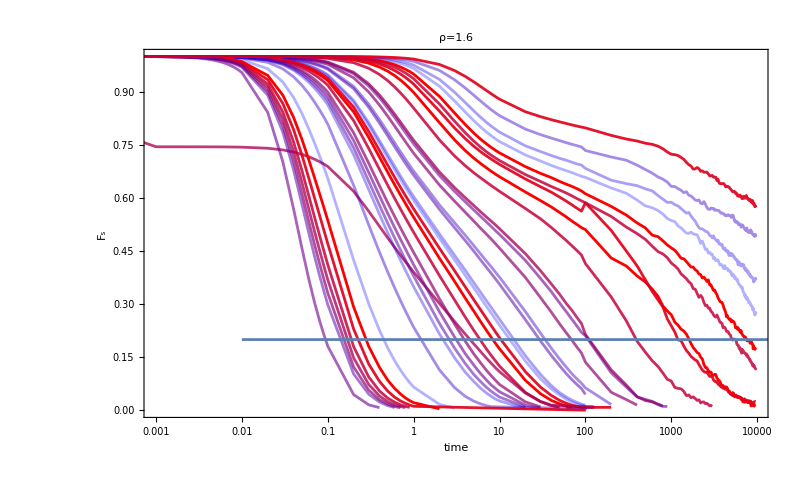
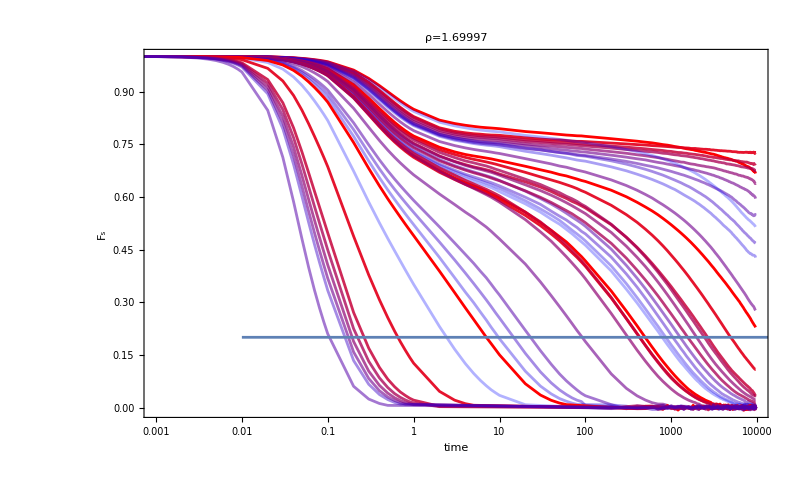
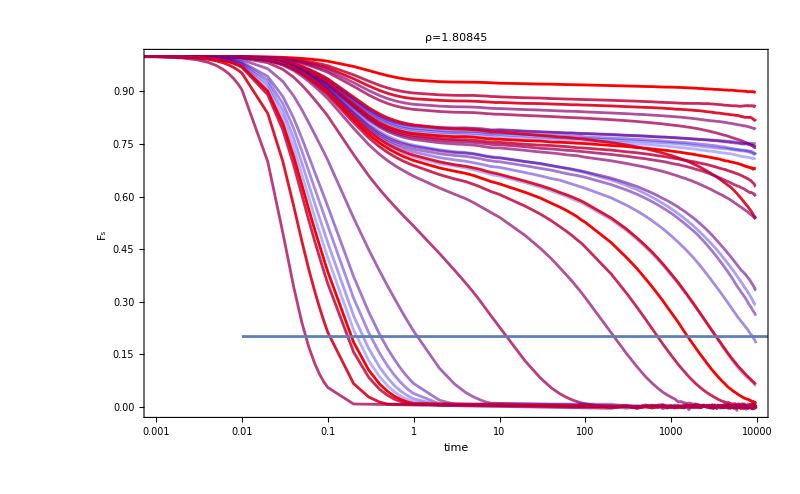
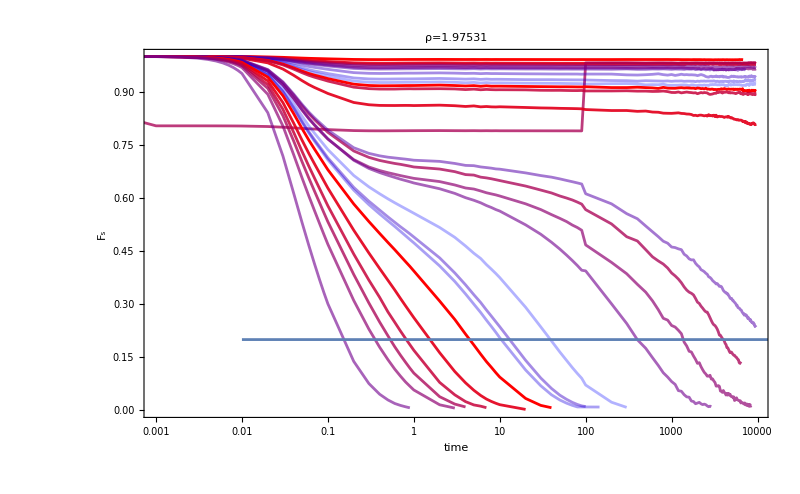

```mathematica
Table[Show[ListLogLinearPlot[fs[[r,;;,;;,1;;2]],ImageSize->800,PlotRange->{{0.001,All},All},PlotStyle->redBluePlotConfig[10],PlotLabel->"ρ="<>ToString[rhoValues[[r]]],Joined->True,FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}]],{r,Length[rhoValues]}]
```

```mathematica
tauAlpha=Table[Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/tauAlpha/tauAlpha_rho"<>ToString[rhoValues[[r]]]<>".csv","Data"][[;;,1]],{r,Length[rhoValues]}];
```

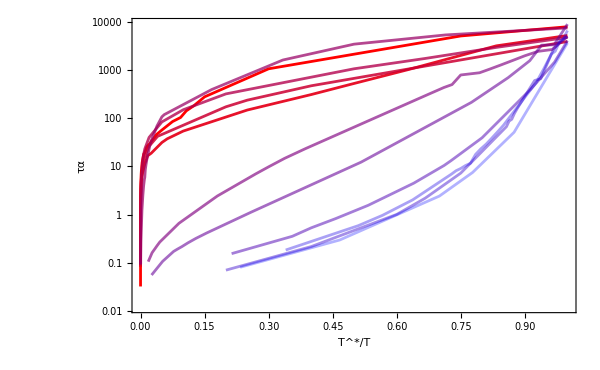

```mathematica
Show[ListLogPlot[Table[Table[{temperatures[[r,Length[tauAlpha[[r]]]]]/temperatures[[r,T]],tauAlpha[[r,T]]},{T,Length[tauAlpha[[r]]]}],{r,Length[rhoValues]}],FrameLabel->{"T^*/T","τα"},ImageSize->600,PlotRange->{All,All},Joined->True,PlotStyle->redBluePlotConfig[Length[rhoValues]]]]
```

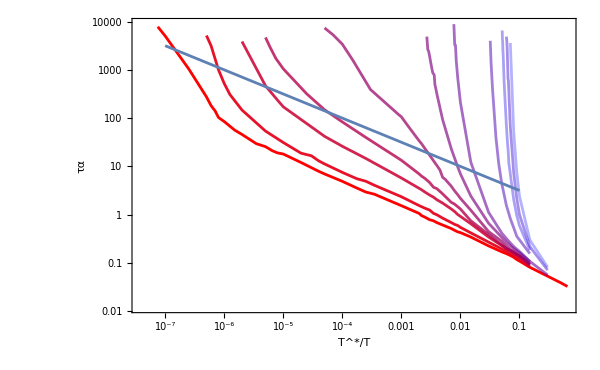

```mathematica
Show[ListLogLogPlot[Table[Table[{temperatures[[r,T]],tauAlpha[[r,T]]},{T,Length[tauAlpha[[r]]]}],{r,Length[rhoValues]}],FrameLabel->{"T^*/T","τα"},ImageSize->600,PlotRange->{All,All},Joined->True,PlotStyle->redBluePlotConfig[Length[rhoValues]]],LogLogPlot[x^-0.5,{x,0.0000001,0.1}]]
```